```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/baryon_number_fluc/mub500data/v3

```mathematica
data=Import["./Shi_T-mu_500.0-flag_4-21x120_VC=true_abstol1e-5.csv"];
```

```mathematica
data[[1]]
```

{T_mu,σ,ω₀,n_B,P,ϵ}

```mathematica
data[[2]][[1]]
```

(0.0, 460.1118481127528)

```mathematica
Head[data[[2]][[1]]]
```

String

```mathematica
StringCases[data[[2]][[1]],NumberString]
```

{0.0,460.1118481127528}

```mathematica
T=ToExpression[Table[StringCases[data[[i]][[1]],NumberString][[1]],{i,2,121}]];
mub=ToExpression[Table[StringCases[data[[i*120+2]][[1]],NumberString][[2]],{i,0,20}]];
p=Table[Table[data[[j*120+i]][[5]],{i,2,121}],{j,0,20}];
```

```mathematica
plotdata=Table[Transpose[{T[[2;;120]],p[[i]][[2;;120]]*197.33^3}],{i,1,21}];
```

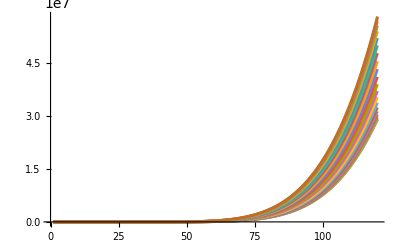

```mathematica
ListLinePlot[plotdata,PlotRange->{All,All}]
```

```mathematica
exportdata=Table[p[[i]][[2;;120]]*197.33^3,{i,1,21}];
```

```mathematica
Table[Export["V"<>ToString[i]<>".dat",p[[i]][[1;;120]]*197.33^3],{i,1,21}]
```

{V1.dat,V2.dat,V3.dat,V4.dat,V5.dat,V6.dat,V7.dat,V8.dat,V9.dat,V10.dat,V11.dat,V12.dat,V13.dat,V14.dat,V15.dat,V16.dat,V17.dat,V18.dat,V19.dat,V20.dat,V21.dat}

```mathematica
Export["T.dat",T]
```

T.dat

```mathematica
mub
```

{460.112,461.003,462.765,465.359,468.727,472.793,477.467,482.645,488.21,494.038,500.,505.962,511.79,517.355,522.533,527.207,531.273,534.641,537.235,538.997,539.888}

```mathematica
Length[T]
```

120

```mathematica
T
```

{0.,1.0084,2.01681,3.02521,4.03361,5.04202,6.05042,7.05882,8.06723,9.07563,10.084,11.0924,12.1008,13.1092,14.1176,15.1261,16.1345,17.1429,18.1513,19.1597,20.1681,21.1765,22.1849,23.1933,24.2017,25.2101,26.2185,27.2269,28.2353,29.2437,30.2521,31.2605,32.2689,33.2773,34.2857,35.2941,36.3025,37.3109,38.3193,39.3277,40.3361,41.3445,42.3529,43.3613,44.3697,45.3782,46.3866,47.395,48.4034,49.4118,50.4202,51.4286,52.437,53.4454,54.4538,55.4622,56.4706,57.479,58.4874,59.4958,60.5042,61.5126,62.521,63.5294,64.5378,65.5462,66.5546,67.563,68.5714,69.5798,70.5882,71.5966,72.605,73.6134,74.6218,75.6303,76.6387,77.6471,78.6555,79.6639,80.6723,81.6807,82.6891,83.6975,84.7059,85.7143,86.7227,87.7311,88.7395,89.7479,90.7563,91.7647,92.7731,93.7815,94.7899,95.7983,96.8067,97.8151,98.8235,99.8319,100.84,101.849,102.857,103.866,104.874,105.882,106.891,107.899,108.908,109.916,110.924,111.933,112.941,113.95,114.958,115.966,116.975,117.983,118.992,120.}

```mathematica
121./120.*2-1
```

1.01667